```mathematica
(*g:=a+b*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]*)
g:=Sqrt[a b]+Sqrt[a b]*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]
h :=(g/.{Subscript[z, j]->Subscript[z, j],Subscript[z, k]->Subscript[z, k]})(g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->1/Subscript[z, j]})/
((g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->Subscript[z, j]})(g/.{Subscript[z, j]->1/Subscript[z, j],Subscript[z, k]->Subscript[z, k]}))
h1:=h/.{Subscript[z, j]->Subscript[z, 1],Subscript[z, k]->Subscript[z, 2]}
h2:=h/.{Subscript[z, j]->Subscript[z, 2],Subscript[z, k]->Subscript[z, 1]}
f1:=(Subscript[z, 1]^8 - h1)/.{a->1,b->2}
f2:=(Subscript[z, 2]^8- h2)/.{a->1,b->2}
(*roots = FindRoot[{f1==0,f2==0}, {{Subscript[z, 1],-1}, {Subscript[z, 2],3}}]*)
roots = Solve[{f1==0,f2==0}, {Subscript[z, 1],Subscript[z, 2]}]//N
```

{{z_1→-1.,z_2→-1.},{z_1→-1.,z_2→1.},{z_1→0.,z_2→0.},{z_1→1.,z_2→-1.},{z_1→1.,z_2→1.},{z_1→0.332423+0.443604 ⅈ,z_2→0.332423-0.443604 ⅈ},{z_1→0.332423+0.443604 ⅈ,z_2→1.08179+1.4436 ⅈ},{z_1→1.08179-1.4436 ⅈ,z_2→0.332423-0.443604 ⅈ},{z_1→1.08179-1.4436 ⅈ,z_2→1.08179+1.4436 ⅈ},{z_1→0.332423-0.443604 ⅈ,z_2→0.332423+0.443604 ⅈ},{z_1→0.332423-0.443604 ⅈ,z_2→1.08179-1.4436 ⅈ},{z_1→1.08179+1.4436 ⅈ,z_2→0.332423+0.443604 ⅈ},{z_1→1.08179+1.4436 ⅈ,z_2→1.08179-1.4436 ⅈ},{z_1→-0.644484-0.764618 ⅈ,z_2→0.29093-0.956744 ⅈ},{z_1→-0.644484-0.764618 ⅈ,z_2→0.29093+0.956744 ⅈ},{z_1→-0.644484+0.764618 ⅈ,z_2→0.29093-0.956744 ⅈ},{z_1→-0.644484+0.764618 ⅈ,z_2→0.29093+0.956744 ⅈ},{z_1→0.29093-0.956744 ⅈ,z_2→-0.644484+0.764618 ⅈ},{z_1→0.29093-0.956744 ⅈ,z_2→-0.644484-0.764618 ⅈ},{z_1→0.29093+0.956744 ⅈ,z_2→-0.644484-0.764618 ⅈ},{z_1→0.29093+0.956744 ⅈ,z_2→-0.644484+0.764618 ⅈ},{z_1→-0.698539-0.715572 ⅈ,z_2→1.},{z_1→-0.698539+0.715572 ⅈ,z_2→1.},{z_1→0.759199-0.650858 ⅈ,z_2→1.},{z_1→0.759199+0.650858 ⅈ,z_2→1.},{z_1→0.301461-0.953478 ⅈ,z_2→-1.},{z_1→0.301461+0.953478 ⅈ,z_2→-1.},{z_1→0.311863,z_2→-1.},{z_1→3.20654,z_2→-1.},{z_1→0.779307,z_2→1.},{z_1→1.28319,z_2→1.},{z_1→-0.614912-0.788596 ⅈ,z_2→-1.},{z_1→-0.614912+0.788596 ⅈ,z_2→-1.},{z_1→0.331123,z_2→-1.},{z_1→3.02002,z_2→-1.},{z_1→0.029411-0.999567 ⅈ,z_2→1.},{z_1→0.029411+0.999567 ⅈ,z_2→1.},{z_1→-0.620302-0.784363 ⅈ,z_2→-0.620302+0.784363 ⅈ},{z_1→-0.620302-0.784363 ⅈ,z_2→-0.620302-0.784363 ⅈ},{z_1→-0.620302+0.784363 ⅈ,z_2→-0.620302-0.784363 ⅈ},{z_1→-0.620302+0.784363 ⅈ,z_2→-0.620302+0.784363 ⅈ},{z_1→0.232899-0.972501 ⅈ,z_2→0.232899+0.972501 ⅈ},{z_1→0.232899-0.972501 ⅈ,z_2→0.232899-0.972501 ⅈ},{z_1→0.232899+0.972501 ⅈ,z_2→0.232899-0.972501 ⅈ},{z_1→0.232899+0.972501 ⅈ,z_2→0.232899+0.972501 ⅈ},{z_1→0.917733-0.397198 ⅈ,z_2→0.917733+0.397198 ⅈ},{z_1→0.917733-0.397198 ⅈ,z_2→0.917733-0.397198 ⅈ},{z_1→0.917733+0.397198 ⅈ,z_2→0.917733-0.397198 ⅈ},{z_1→0.917733+0.397198 ⅈ,z_2→0.917733+0.397198 ⅈ},{z_1→1.,z_2→-0.698539-0.715572 ⅈ},{z_1→1.,z_2→-0.698539+0.715572 ⅈ},{z_1→1.,z_2→0.759199-0.650858 ⅈ},{z_1→1.,z_2→0.759199+0.650858 ⅈ},{z_1→-1.,z_2→0.301461-0.953478 ⅈ},{z_1→-1.,z_2→0.301461+0.953478 ⅈ},{z_1→-1.,z_2→0.311863},{z_1→-1.,z_2→3.20654},{z_1→1.,z_2→0.779307},{z_1→1.,z_2→1.28319},{z_1→-1.,z_2→-0.614912-0.788596 ⅈ},{z_1→-1.,z_2→-0.614912+0.788596 ⅈ},{z_1→-1.,z_2→0.331123},{z_1→-1.,z_2→3.02002},{z_1→1.,z_2→0.029411-0.999567 ⅈ},{z_1→1.,z_2→0.029411+0.999567 ⅈ}}

```mathematica
a=1;b=2;
(*ev:=(b(Subscript[z, 1]+Subscript[z, 2])+a(Subscript[z, 1]^-1+Subscript[z, 2]^-1)-2(a+b))/.roots*)
ev:=(Sqrt[a b](Subscript[z, 1]+Subscript[z, 2])+Sqrt[a b](Subscript[z, 1]^-1+Subscript[z, 2]^-1)-2(a+b))/.roots
Re[ev]
{(Re[Subscript[z, 1]]-Re[Subscript[z, 2]])(Abs[Re[Subscript[z, 1]]]-1)(Abs[Re[Subscript[z, 2]]]-1)}/.roots
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{-11.6569,-6.,Indeterminate,-6.,-0.343146,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-7.,-7.,-7.,-7.,-7.,-7.,-7.,-7.,-5.14734,-5.14734,-1.02423,-1.02423,-7.97577,-7.97577,-3.85266,-3.85266,-0.25476,-0.25476,-10.5677,-10.5677,-4.08919,-4.08919,-3.08839,-3.08839,-9.50896,-9.50896,-9.50896,-9.50896,-4.68253,-4.68253,-4.68253,-4.68253,-0.808517,-0.808517,-0.808517,-0.808517,-5.14734,-5.14734,-1.02423,-1.02423,-7.97577,-7.97577,-3.85266,-3.85266,-0.25476,-0.25476,-10.5677,-10.5677,-4.08919,-4.08919,-3.08839,-3.08839}

{{0.},{0.},{0.},{0.},{0.},{4.94781×10^-17},{0.0409168},{-0.0409168},{8.19508×10^-15},{4.94781×10^-17},{0.0409168},{-0.0409168},{8.19508×10^-15},{-0.235805},{-0.235805},{-0.235805},{-0.235805},{0.235805},{0.235805},{0.235805},{0.235805},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{4.80185×10^-17},{0.},{4.80185×10^-17},{0.},{0.},{0.},{0.},{0.},{-1.50276×10^-18},{7.51381×10^-19},{-1.50276×10^-18},{7.51381×10^-19},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{-11.6569,-6.,Indeterminate,-6.,-0.343146,-1.58579,-1.58579,-4.41421,-4.41421,-1.29844,-1.29844,-1.29844,-1.29844,-7.70156,-7.70156,-7.70156,-7.70156,-9.5998,-9.5998,-3.64284,-3.64284,-4.53012,-4.53012,-0.227243,-0.227243,-1.58579,-1.58579,-4.41421,-4.41421,-9.5998,-9.5998,-3.64284,-3.64284,-4.53012,-4.53012,-0.227243,-0.227243}

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{-3.16616×10^-18},{-6.33232×10^-18},{-3.16616×10^-18},{-6.33232×10^-18},{-8.14158×10^-17},{-1.35693×10^-16},{-8.14158×10^-17},{-1.35693×10^-16},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

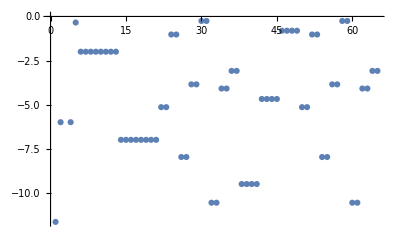

```mathematica
ListPlot[Re[ev]]
```

```mathematica
M := Transpose[{{-a, a, 0, 0, 0, 0}, {b, -2*a-b, a, a, 0, 0}, {0, b, -a-b, 0, a, 0}, {0, b, 0, -a-b, a, 0},
 {0, 0, b, b, -a-2*b, a},{0, 0, 0, 0, b, -b}}]
Eigensystem[M]
Eigenvalues[M/.{a->1, b->2}]//N
```

{{-7,-5,-3,-2,-1,0},{{2,-6,4,4,-5,1},{-4,8,-1,-1,-3,1},{0,0,-1,1,0,0},{2,-1,-1,-1,0,1},{-4,0,1,1,1,1},{16,8,4,4,2,1}}}

{-7.,-5.,-3.,-2.,-1.,0.}

```mathematica
{(Re[Subscript[z, 1]]-Re[Subscript[z, 2]])(Abs[Re[Subscript[z, 1]]]-1)(Abs[Re[Subscript[z, 2]]]-1)}/.roots
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{-3.16616×10^-18},{-6.33232×10^-18},{-3.16616×10^-18},{-6.33232×10^-18},{-8.14158×10^-17},{-1.35693×10^-16},{-8.14158×10^-17},{-1.35693×10^-16},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
(*g:=a+b*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]*)
g:=Sqrt[a b]+Sqrt[a b]*Subscript[z, j]*Subscript[z, k]-(a+b)*Subscript[z, j]
h :=(g/.{Subscript[z, j]->Subscript[z, j],Subscript[z, k]->Subscript[z, k]})(g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->1/Subscript[z, j]})/
((g/.{Subscript[z, j]->Subscript[z, k],Subscript[z, k]->Subscript[z, j]})(g/.{Subscript[z, j]->1/Subscript[z, j],Subscript[z, k]->Subscript[z, k]}))
h1:=h/.{Subscript[z, j]->Subscript[z, 1],Subscript[z, k]->Subscript[z, 2]}
h2:=h/.{Subscript[z, j]->Subscript[z, 2],Subscript[z, k]->Subscript[z, 1]}
f1:=(Subscript[z, 1]^6 - h1)/.{a->1,b->2}
f2:=(Subscript[z, 2]^6- h2)/.{a->1,b->2}
(*roots = FindRoot[{f1==0,f2==0}, {{Subscript[z, 1],-1}, {Subscript[z, 2],3}}]*)
roots = Solve[{f1==0,f2==0}, {Subscript[z, 1],Subscript[z, 2]}]//N
a=1;b=2;
(*ev:=(b(Subscript[z, 1]+Subscript[z, 2])+a(Subscript[z, 1]^-1+Subscript[z, 2]^-1)-2(a+b))/.roots*)
ev:=(Sqrt[a b](Subscript[z, 1]+Subscript[z, 2])+Sqrt[a b](Subscript[z, 1]^-1+Subscript[z, 2]^-1)-2(a+b))/.roots
Re[ev]
```

{{z_1→-1.,z_2→-1.},{z_1→-1.,z_2→1.},{z_1→0.,z_2→0.},{z_1→1.,z_2→-1.},{z_1→1.,z_2→1.},{z_1→0.56066-0.828046 ⅈ,z_2→1.},{z_1→0.56066+0.828046 ⅈ,z_2→1.},{z_1→0.36247,z_2→-1.},{z_1→2.75885,z_2→-1.},{z_1→0.831127-0.556083 ⅈ,z_2→0.831127-0.556083 ⅈ},{z_1→0.831127-0.556083 ⅈ,z_2→0.831127+0.556083 ⅈ},{z_1→0.831127+0.556083 ⅈ,z_2→0.831127+0.556083 ⅈ},{z_1→0.831127+0.556083 ⅈ,z_2→0.831127-0.556083 ⅈ},{z_1→-0.300797-0.953688 ⅈ,z_2→-0.300797+0.953688 ⅈ},{z_1→-0.300797-0.953688 ⅈ,z_2→-0.300797-0.953688 ⅈ},{z_1→-0.300797+0.953688 ⅈ,z_2→-0.300797-0.953688 ⅈ},{z_1→-0.300797+0.953688 ⅈ,z_2→-0.300797+0.953688 ⅈ},{z_1→-0.27272-0.962093 ⅈ,z_2→-1.},{z_1→-0.27272+0.962093 ⅈ,z_2→-1.},{z_1→0.296733,z_2→-1.},{z_1→3.37003,z_2→-1.},{z_1→-0.480318-0.877095 ⅈ,z_2→1.},{z_1→-0.480318+0.877095 ⅈ,z_2→1.},{z_1→0.751781,z_2→1.},{z_1→1.33017,z_2→1.},{z_1→1.,z_2→0.56066-0.828046 ⅈ},{z_1→1.,z_2→0.56066+0.828046 ⅈ},{z_1→-1.,z_2→0.36247},{z_1→-1.,z_2→2.75885},{z_1→-1.,z_2→-0.27272-0.962093 ⅈ},{z_1→-1.,z_2→-0.27272+0.962093 ⅈ},{z_1→-1.,z_2→0.296733},{z_1→-1.,z_2→3.37003},{z_1→1.,z_2→-0.480318-0.877095 ⅈ},{z_1→1.,z_2→-0.480318+0.877095 ⅈ},{z_1→1.,z_2→0.751781},{z_1→1.,z_2→1.33017}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

{-11.6569,-6.,Indeterminate,-6.,-0.343146,-1.58579,-1.58579,-4.41421,-4.41421,-1.29844,-1.29844,-1.29844,-1.29844,-7.70156,-7.70156,-7.70156,-7.70156,-9.5998,-9.5998,-3.64284,-3.64284,-4.53012,-4.53012,-0.227243,-0.227243,-1.58579,-1.58579,-4.41421,-4.41421,-9.5998,-9.5998,-3.64284,-3.64284,-4.53012,-4.53012,-0.227243,-0.227243}

```mathematica
{Arg[Subscript[z, 1]],Arg[Subscript[z, 2]]}/.roots
```

{{π,π},{π,0},{0,0},{0,π},{0,0},{-0.975613,0},{0.975613,0},{0,π},{0,π},{-0.589666,-0.589666},{-0.589666,0.589666},{0.589666,0.589666},{0.589666,-0.589666},{-1.87632,1.87632},{-1.87632,-1.87632},{1.87632,-1.87632},{1.87632,1.87632},{-1.84702,π},{1.84702,π},{0,π},{0,π},{-2.07181,0},{2.07181,0},{0,0},{0,0},{0,-0.975613},{0,0.975613},{π,0},{π,0},{π,-1.84702},{π,1.84702},{π,0},{π,0},{0,-2.07181},{0,2.07181},{0,0},{0,0}}

(-2 (√(p^3 q)+√(p q^3))+p (p+3 q) z_k+z_j (q (3 p+q)-2 (√(p^3 q)+√(p q^3)) z_k))/(-2 (√(p^3 q)+√(p q^3))+q (3 p+q) z_k+z_j (p (p+3 q)-2 (√(p^3 q)+√(p q^3)) z_k))

```mathematica
g1:=p+q*Subscript[z, j]*Subscript[z, k]-(p+q)*Subscript[z, j]
g2:=Sqrt[p q]+Sqrt[p q]*Subscript[z, j]*Subscript[z, k]-(p+q)*Subscript[z, j]
Simplify[(Sqrt[q/p]g1)/.{Subscript[z, j]->(Sqrt[p/q] Subscript[z, j]),Subscript[z, k]->(Sqrt[p/q] Subscript[z, k])},{p>0, q>0}]
```

√(q/p) (p-√(p/q) (p+q) z_j+p z_j z_k)

```mathematica
Sqrt[1/2]//N
```

0.707107